```mathematica
Clear[β,b]
```

```mathematica
Series[-(1/β)Log[2 Cosh[4β J2 m+4β J4 m^3]]+2 J2 m^2+3 J4 m^4,{m,0,6}]
```

-Log[2]/β+(2 J2-8 J2^2 β) m^2+(3 J4-16 J2 J4 β+(64 J2^4 β^3)/3) m^4+(-8 J4^2 β+256/3 J2^3 J4 β^3-(4096 J2^6 β^5)/45) m^6+O[m]^7

```mathematica
Series[-(4/β)Log[2 Cosh[β (m+ J m^3)]]+2 m^2+3 J m^4,{m,0,6}]
```

-(4 Log[2])/β+(2-2 β) m^2+(3 J-4 J β+β^3/3) m^4+(-2 J^2 β+(4 J β^3)/3-(4 β^5)/45) m^6+O[m]^7

```mathematica
Solve[4β-3==β^3&&β>0,β ]
```

{{β→1},{β→1/2 (-1+√13)}}

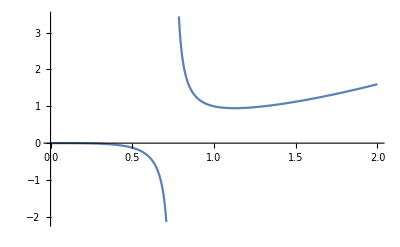

```mathematica
Plot[β^3/(4β-3),{β,0,2}]
```

```mathematica
FullSimplify[(3 J4-4 J4 β+β^3/3)^2== -(2-2 β) (-2 J4^2 β+(4 J4 β^3)/3-(4 β^5)/45)/3]
```

30 J4 (13-16 β) β^3+β^5 (-8+23 β)+45 J4^2 (27-76 β+52 β^2)==0

```mathematica
Solve[(3 J4-4 J4 β+β^3/3)^2== -(2-2 β) (-2 J4^2 β+(4 J4 β^3)/3-(4 β^5)/45)/3,J4]
```

{{J4→(-13 β^3+16 β^4-2 √(3/5) √(18 β^5-32 β^6+7 β^7+7 β^8))/(3 (27-76 β+52 β^2))},{J4→(-13 β^3+16 β^4+2 √(3/5) √(18 β^5-32 β^6+7 β^7+7 β^8))/(3 (27-76 β+52 β^2))}}

```mathematica
(*Show[%54,ImageSize->Large],*)
Manipulate[
Plot[{x,Tanh[a (x+b x^3)]},{x,-1,1}],
{a,0.1,3},{b,0.1,3}]
```

```mathematica
Series[Tanh[β(m+J4 m^3)],{m,0,4}]
```

β m+(J4 β-β^3/3) m^3+O[m]^5

```mathematica
a2[β_,J_]:=4(1-β);
a4[β_,J_]:=4(3 J-4J β+β^3/3);
a6[β_,J_]:=6(-2 J^2 β+4J β^3/3-4 β^5/45);
```

```mathematica
a2[β,J]
a4[β,J]
a6[β,J]
```

4 (1-β)

4 (3 J-4 J β+β^3/3)

6 (-2 J^2 β+(4 J β^3)/3-(4 β^5)/45)

```mathematica
b=1;
j=1/3;
3 a4[b,j]^2-a2[b,j] a6[b,j]
```

0

```mathematica
FullSimplify[a2[β,J]*a6[β,J]]
```

16/15 (-1+β) (45 J^2 β-30 J β^3+2 β^5)

```mathematica
Expand[3 a4[β,J]^2==a2[β,J] a6[β,J]]
FullSimplify[3 a4[β,J]^2==a2[β,J] a6[β,J]]
FullSimplify[Solve[3 a4[b,J]^2==a2[b,J] a6[b,J],J]]
```

432 J^2-1152 J^2 β+768 J^2 β^2+96 J β^3-128 J β^4+(16 β^6)/3==-48 J^2 β+48 J^2 β^2+32 J β^3-32 J β^4-(32 β^5)/15+(32 β^6)/15

30 J (2-3 β) β^3+β^5 (2+3 β)+45 J^2 (9+β (-23+15 β))==0

{{J→(5 b^3 (-2+3 b)-√15 √(-(-1+b) b^5 (-6+7 b)))/(15 (9+b (-23+15 b)))},{J→(5 b^3 (-2+3 b)+√15 √(-(-1+b) b^5 (-6+7 b)))/(15 (9+b (-23+15 b)))}}

```mathematica
Solve[-(-1+β) β^5 (-6+7 β)==0]
```

{{β→0},{β→0},{β→0},{β→0},{β→0},{β→6/7},{β→1}}

```mathematica
Expand[a4[β,J]==-√(a2[β,J] a6[β,J])/3]
```

12 J-16 J β+(4 β^3)/3==-2 √(2/3) √((1-β) (-2 J^2 β+(4 J β^3)/3-(4 β^5)/45))

```mathematica
FullSimplify[Solve[a4[β,J]==-√(a2[β,J] a6[β,J]/3),J]]
```

{{J→(5 β^3 (-2+3 β)-√15 √(-(-1+β) β^5 (-6+7 β)))/(15 (9+β (-23+15 β)))},{J→(5 β^3 (-2+3 β)+√15 √(-(-1+β) β^5 (-6+7 β)))/(15 (9+β (-23+15 β)))}}

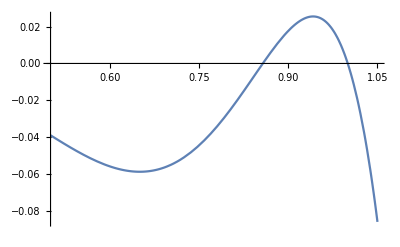

```mathematica
Plot[-(-1+β) β^5 (-6+7 β),{β,0.5,1.05}]
```

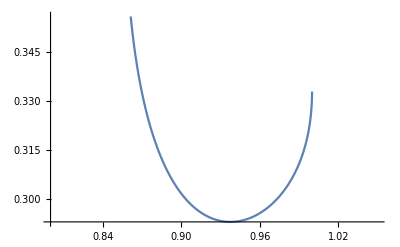

```mathematica
Plot[(5 β^3 (-2+3 β)-√15 √(-(-1+β) β^5 (-6+7 β)))/(15 (9+β (-23+15 β))),{β,0.8,1.05}]
```

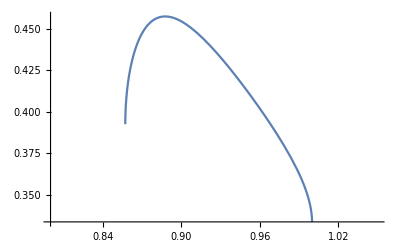

```mathematica
Plot[(5 β^3 (-2+3 β)+√15 √(-(-1+β) β^5 (-6+7 β)))/(15 (9+β (-23+15 β))),{β,0.8,1.05}]
```

```mathematica
FullSimplify[Solve[a4[1/4T,J]==-√(a2[1/4T,J] a6[1/4T,J]/3),J]]
```

{{J→(5 T^3 (-8+3 T)-2 √15 √(-(-4+T) T^5 (-24+7 T)))/(240 (144+T (-92+15 T)))},{J→(5 T^3 (-8+3 T)+2 √15 √(-(-4+T) T^5 (-24+7 T)))/(240 (144+T (-92+15 T)))}}

```mathematica
Solve[3 a4[1/4T,J]^2-a2[1/4T,J] a6[1/4T,J]==0,J]
```

{{J→(-8 T^3+3 T^4-2 √(3/5) √(-96 T^5+52 T^6-7 T^7))/(48 (144-92 T+15 T^2))},{J→(-8 T^3+3 T^4+2 √(3/5) √(-96 T^5+52 T^6-7 T^7))/(48 (144-92 T+15 T^2))}}

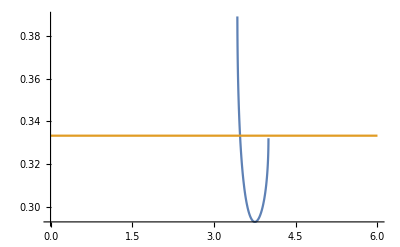

```mathematica
Plot[{(5 T^3 (-8+3 T)-2 √15 √(-(-4+T) T^5 (-24+7 T)))/(240 (144+T (-92+15 T))),1/3},{T,0,6}]
```

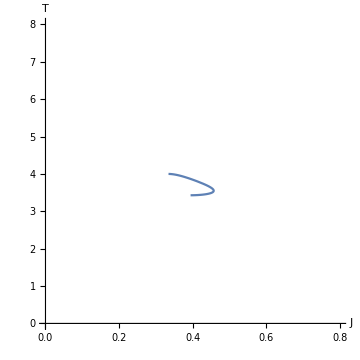

```mathematica
ParametricPlot[{(5 T^3 (-8+3 T)+2 √15 √(-(-4+T) T^5 (-24+7 T)))/(240 (144+T (-92+15 T))),T},{T,0,6},AxesLabel->{"J","T"},PlotRange->{{0,0.8},{0,8}},AspectRatio->1,ImageSize->Medium]
```

```mathematica
Solve[3 a4[1/4T,J]^2-a2[1/4T,J] a6[1/4T,J]==0,T]
```

{{T→Root[1658880 J^2-1059840 J^2 #1+172800 J^2 #1^2+3840 J #1^3-1440 J #1^4+8 #1^5+3 #1^6&,1]},{T→Root[1658880 J^2-1059840 J^2 #1+172800 J^2 #1^2+3840 J #1^3-1440 J #1^4+8 #1^5+3 #1^6&,2]},{T→Root[1658880 J^2-1059840 J^2 #1+172800 J^2 #1^2+3840 J #1^3-1440 J #1^4+8 #1^5+3 #1^6&,3]},{T→Root[1658880 J^2-1059840 J^2 #1+172800 J^2 #1^2+3840 J #1^3-1440 J #1^4+8 #1^5+3 #1^6&,4]},{T→Root[1658880 J^2-1059840 J^2 #1+172800 J^2 #1^2+3840 J #1^3-1440 J #1^4+8 #1^5+3 #1^6&,5]},{T→Root[1658880 J^2-1059840 J^2 #1+172800 J^2 #1^2+3840 J #1^3-1440 J #1^4+8 #1^5+3 #1^6&,6]}}